```mathematica
<<Vilcretas`
```

VilCretas está disponible.

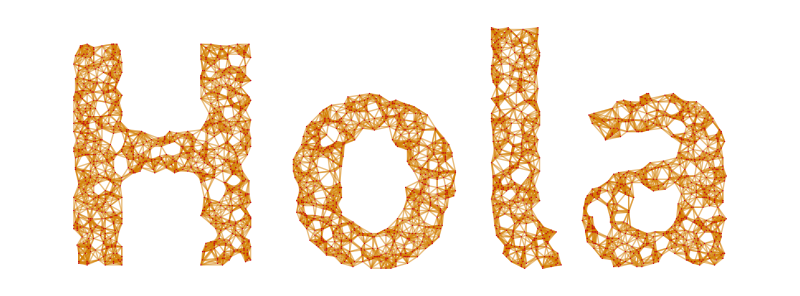

```mathematica
GrafoString["Hola"]
```

```mathematica
f=Product[3^i/(i+1)^2,{i,2,n-2}];
g=3^(n^2)n!;
```

```mathematica
Limit[f/g, n->Infinity]
```

0

```mathematica
Clear[f]
```

```mathematica
Clear[g]
```

```mathematica
f[n_]:=Module[{s=0,i},
For[i=5, i<= 2n-3,i++, s=s+(i+1)^2];
s]
```

```mathematica
g[n_]:=If[n<4,0,1/3(-168+13n-18n^2+8n^3)]
```

```mathematica
{f[200], g[200]}
```

{21094144,21094144}

```mathematica
PruebaADAGrafica[{f,g},30,2,2]
```

-Graphics-

```mathematica
SumatoriaRandom[3,vectorial->True]
Sumatoria[%]
SumatoriaCola[%%]
```

{1,-1+n,(1+6 i^2)/(-2+3 i^4+20 i^5)}

Sumatoria[n_]:=If[n==2,1/3,Sumatoria[n-1]+((1+6 (-1+n)^2)/(-2+3 (-1+n)^4+20 (-1+n)^5))]

SumatoriaCola[n_,suma_:1/3]:=If[n==2,suma,SumatoriaCola[n-1,suma+((1+6 (-1+n)^2)/(-2+3 (-1+n)^4+20 (-1+n)^5))]]

```mathematica
SumaCuad1[n_]:=Total[IntegerDigits[n]^2]
SumaCuad2[n_]:=Module[{m=IntegerDigits[n],i,suma=0},For[i=1,i<=Length[m],suma=suma+m[[i]]^2;i++];
suma]
SumaCuad3[n_]:=Module[{suma=Mod[n,10]},If[n==0,Return[suma],suma^2+SumaCuad3[(n-Mod[n,10])/10]]]
SumaCuad4[n_]:=Module[{suma=0,m=n,digito},While[m!=0,digito=Mod[m,10];
suma=suma+digito^2;
m=(m-digito)/10;];
suma]
```

```mathematica
PruebaADAGrafica[{SumaCuad1, SumaCuad2, SumaCuad3, SumaCuad4}, 20,1,3]
```

-Graphics-

```mathematica
Clear[f]
```

```mathematica
Clear[g]
```

```mathematica
f=(n^2+n+3^n)(n^n+3^n+1);
```

```mathematica
g={(3+n)^n,(n!)^n,(2n)^n, (3n)^n};
```

```mathematica
Table[Limit[f/i, n->Infinity],{i,g}]
```

{∞,0,∞,1}

```mathematica
Table[i->Limit[f/i, n->Infinity],{i,g}]
```

{(3+n)^n→∞,(n!)^n→0,2^n n^n→∞,3^n n^n→1}

```mathematica
Limit[f/(3n)^n, n->Infinity]
```

1

```mathematica
Clear[f]
```

```mathematica
Clear[g]
```

```mathematica
f=Product[1-1/(i+1),{i,7,n+2}];
```

```mathematica
g=(j*n^9)/(j*n^j+3);
```

```mathematica
CompLimit[{f,g}]
```

```mathematica
Table[j->Limit[f/g, n->Infinity], {j,15}]
```

{1→0,2→0,3→0,4→0,5→0,6→0,7→0,8→0,9→0,10→7,11→∞,12→∞,13→∞,14→∞,15→∞}

```mathematica
Clear[f]
```

```mathematica
f = Sum[Sum[Sum[1,{k,1,(i+j)/2}], {j,1,i/2}],{i,1,2n}];
```

```mathematica
g = {Log[n], n, n Log[n],Log2[n], n^3};
```

```mathematica
Table[i->Limit[f/i, n->Infinity], {i,g}]
```

{Log[n]→∞,n→∞,n Log[n]→∞,Log[n]/Log[2]→∞,n^3→5/6}

Theta = O Grande y Omega(Debe ser ambas, no solamente una)
0 -> O Grande
+Infinito -> Omega
Real Positivo -> Theta
Negativos -> Ninguno

```mathematica
Clear[f]
```

```mathematica
Clear[g]
```

```mathematica
f = Sum[-8 i^4+17^(17i)+16,{i,1,n-2}];
g = {17^(17n),n^9,n^7,n^8};
```

```mathematica
Table[i->Limit[f/i, n->Infinity],{i,g}]
```

{17^(17 n)→1/684326450885775034048119479663868573723152,n^9→∞,n^7→∞,n^8→∞}